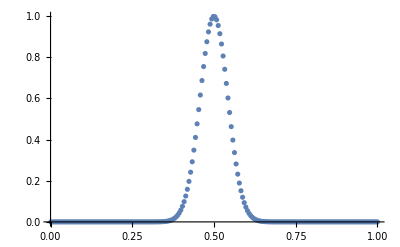

```mathematica
c=3*10^8;
ω0 = 500*10^12;
ωl=1*10^12; ωh=1000*10^12;
Nf=201;
sw=100*10^12; (* spectral width *)
ω=N[Range[ωl,ωh,(ωh-ωl)/Nf]];
A[ω_,ω0_,sw_]:=Exp[-4*Log[2]((ω-ω0)/sw)^2];
Ak=A[ω,ω0,sw];
ListPlot[Transpose[{ω,Ak}],PlotRange->All]
```

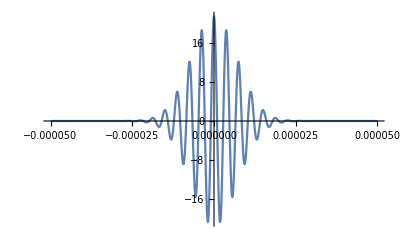

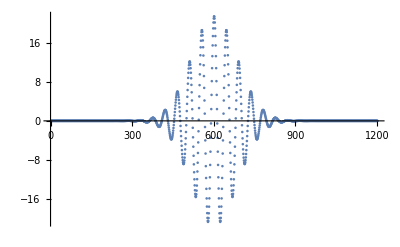

```mathematica
Ext[t_]:=Ak.Cos[ω /c t]
tl=-5*10^-5; th=5*10^-5; Nt=1201;
Plot[Ext[t], {t,tl,th},PlotRange->All]
ts=Range[tl,th,(th-tl)/Nt];
Ets=Map[Ext,ts];
ListPlot[Ets,PlotRange->All]
```

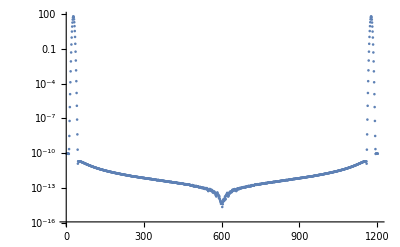

```mathematica
Ew=Fourier[Ets];
ListLogPlot[Abs[Ew]]
```

## Gaussian Beam

-Graphics-

```mathematica
Erz[r_,z_]:=E0 w0/w[z] Exp[-r^2/w[z]^2]Exp[-I(ω/c z+ω/c r^2/(2R[z]))]
InverseFourierTransform[Erz[r,z],ω,t]
```

(2 ⅇ^(-r^2/w[z]^2) E0 √(2 π) w0 DiracDelta[2 t+(2 z)/c+r^2/(c R[z])])/w[z]

## Chi(3)

```mathematica
ϵ0=VacuumPermittivity 
c=SpeedOfLight
chi3[n2_,n0_]:=(4 n0^2 ϵ0 c)/3 n2
UnitConvert[chi3[Quantity[10^-20,"Meters"^2/"Watts"],1]]
```

(625000 Ampere Second)/(22468879468420441 Meter π Volt)

(299792458 Meter)/Second

```mathematica
N[(Ampere (Quantity[1/(8993773740000000000000 π), ("Meters")^2/("Watts")]))/Volt]
```

(Ampere (3.53922×10^-23 m^2/W))/Volt

(Ampere (1/(8993773740000000000000 π) m^2/W))/Volt

```mathematica
Et[t_]:=A Exp[-I ω0 t]
Kerr[Et_]:=ϵ0(χ1+3/4 χ3 Abs[Et]^2)Et
Ew=FourierTransform[Kerr[Et[t]],t,ω,Assumptions->A∈Reals&&ω0∈Reals&&ϵ0∈Reals&&χ1∈Reals&&χ3∈Reals]
TraditionalForm[Simplify[Ew]]
```

A √(2 π) ϵ0 χ1 DiracDelta[ω-ω0]+3/2 A √(π/2) ϵ0 χ3 Abs[A]^2 DiracDelta[ω-ω0]

3/2 √(π/2) A χ3 ϵ0 Abs[A]^2 ω-ω0+√(2 π) A χ1 ϵ0 ω-ω0

## Levenberg-Marquardt Stuff

```mathematica
ClearAll["Global`*"];
(*Pnl[x_]:=3/4 χ3*x^3*)
f[x_]:=Sqrt[(A.x+Pnl[x]-b).(A.x+Pnl[x]-b)]
J=Simplify[D[f[x],{x}]]
H=D[f[x],{x,2}]
```

((-b+A.x+Pnl[x]).(A.1+Pnl'[x])+(A.1+Pnl'[x]).(-b+A.x+Pnl[x]))/(2 √((-b+A.x+Pnl[x]).(-b+A.x+Pnl[x])))

-((-b+A.x+Pnl[x]).(A.1+Pnl'[x])+(A.1+Pnl'[x]).(-b+A.x+Pnl[x]))^2/(4 ((-b+A.x+Pnl[x]).(-b+A.x+Pnl[x]))^(3/2))+((-b+A.x+Pnl[x]).Pnl''[x]+2 (A.1+Pnl'[x]).(A.1+Pnl'[x])+Pnl''[x].(-b+A.x+Pnl[x]))/(2 √((-b+A.x+Pnl[x]).(-b+A.x+Pnl[x])))